## Wobbling frequency

## Analyzing Ω^4+BΩ^2+C

```mathematica
ClearAll["Global`*"]
```

### Working with (Ā)_k=ℐ_0 A_k

```mathematica
bar[I0_,Ak_]:=I0*Ak;
(* the intrinsic terms with I *)
Subscript[P, 31][I_,j_,I0_,A1_,A3_]:=(2I-1)(bar[I0,A3]-bar[I0,A1])+2j*bar[I0,A1];
Subscript[P, 21][I_,j_,I0_,A1_,A2_]:=(2I-1)(bar[I0,A2]-bar[I0,A1])+2j*bar[I0,A1];
(* the single-particle terms with j *)
Subscript[Q, 31][I_,j_,I0_,A1_,A3_]:=(2j-1)(bar[I0,A3]-bar[I0,A1])+2I*bar[I0,A1];
Subscript[Q, 21][I_,j_,I0_,A1_,A2_]:=(2j-1)(bar[I0,A2]-bar[I0,A1])+2I*bar[I0,A1];
(* the triaxial terms *)
Subscript[G, 1][j_,γ_]:=((2j-1)/(j(j+1)))Sqrt[3](Sqrt[3]Cos[γ*π/180]+Sin[γ*π/180]);
Subscript[G, 2][j_,γ_]:=((2j-1)/(j(j+1)))2Sqrt[3]Sin[γ*π/180];
```

## Numerical case

### C=0

```mathematica
Subscript[A, 1]=0.1;
Subscript[A, 2]=1.5;
Subscript[A, 3]=3.5;
Subscript[j, 0]=13/2;
Subscript[γ, 0]=25;
Spin=35/2;
```

```mathematica
Subscript[f, 1][I0_,V_]:=Subscript[P, 31][Spin,Subscript[j, 0],I0,Subscript[A, 1],Subscript[A, 3]]*Subscript[G, 1][Subscript[j, 0],Subscript[γ, 0]]*V+1/I0(Subscript[P, 31][Spin,Subscript[j, 0],I0,Subscript[A, 1],Subscript[A, 3]]*Subscript[Q, 31][Spin,Subscript[j, 0],I0,Subscript[A, 1],Subscript[A, 3]]-4Spin*Subscript[j, 0]*bar[I0,Subscript[A, 3]]^2);
Subscript[f, 2][I0_,V_]:=Subscript[P, 21][Spin,Subscript[j, 0],I0,Subscript[A, 1],Subscript[A, 2]]*Subscript[G, 2][Subscript[j, 0],Subscript[γ, 0]]*V+1/I0(Subscript[P, 21][Spin,Subscript[j, 0],I0,Subscript[A, 1],Subscript[A, 2]]*Subscript[Q, 21][Spin,Subscript[j, 0],I0,Subscript[A, 1],Subscript[A, 2]]-4Spin*Subscript[j, 0]*bar[I0,Subscript[A, 2]]^2);
Subscript[S, 01][I0_,V_]:=(4Spin*Subscript[j, 0]*bar[I0,Subscript[A, 3]]^2-Subscript[P, 31][Spin,Subscript[j, 0],I0,Subscript[A, 1],Subscript[A, 3]]*Subscript[Q, 31][Spin,Subscript[j, 0],I0,Subscript[A, 1],Subscript[A, 3]])/(Subscript[P, 31][Spin,Subscript[j, 0],I0,Subscript[A, 1],Subscript[A, 3]]*Subscript[G, 1][Subscript[j, 0],Subscript[γ, 0]]);
Subscript[S, 02][I0_,V_]:=(4Spin*Subscript[j, 0]*bar[I0,Subscript[A, 2]]^2-Subscript[P, 21][Spin,Subscript[j, 0],I0,Subscript[A, 1],Subscript[A, 2]]*Subscript[Q, 21][Spin,Subscript[j, 0],I0,Subscript[A, 1],Subscript[A, 2]])/(Subscript[P, 21][Spin,Subscript[j, 0],I0,Subscript[A, 1],Subscript[A, 2]]*Subscript[G, 2][Subscript[j, 0],Subscript[γ, 0]]);
Solve[Subscript[f, 1][x,V]==0,V][[1,1]]
Solve[Subscript[f, 2][x,V]==0,V][[1,1]]
```

V→3.97859

V→1.76371

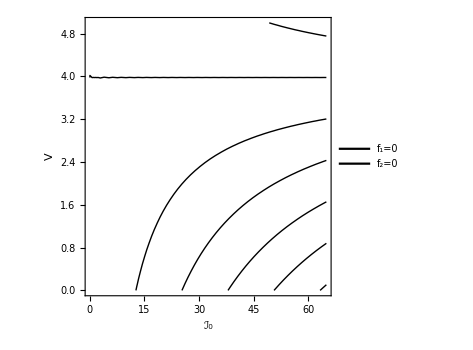

```mathematica
cpf1=ContourPlot[Subscript[f, 1][x,y],{x,0,65},{y,0,5},ContourShading->None,FrameStyle->Directive[Black,Thick],AspectRatio->1,Axes->False,FrameLabel->{"ℐ_0","V"},ImageSize->350,LabelStyle->{18,Black,Bold,FontFamily->"Arial"},PlotLegends->Placed[{"f_1=0","f_2=0"},{0.7,0.8}],PlotRange->Full];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/f1f2_solutions.pdf",Show[cpf1]];
Show[cpf1]
```

### B=0

```mathematica
(*Subscript[F, 1][I0_,V_]:=Subscript[G, 1][Subscript[j, 0],Subscript[γ, 0]]*Subscript[G, 2][Subscript[j, 0],Subscript[γ, 0]]*(I0*V)^2+(Subscript[Q, 21][Subscript[I, 0],Subscript[j, 0],Subscript[ℐ, 0],Subscript[A, 1],Subscript[A, 2]]*Subscript[G, 1][Subscript[j, 0],Subscript[γ, 0]]+Subscript[Q, 31][Subscript[I, 0],Subscript[j, 0],Subscript[ℐ, 0],Subscript[A, 1],Subscript[A, 3]]*Subscript[G, 2][Subscript[j, 0],Subscript[γ, 0]])*(I0*V)^1+Subscript[P, 31][Subscript[I, 0],Subscript[j, 0],Subscript[ℐ, 0],Subscript[A, 1],Subscript[A, 3]]*Subscript[P, 21][Subscript[I, 0],Subscript[j, 0],Subscript[ℐ, 0],Subscript[A, 1],Subscript[A, 2]]+8 Subscript[I, 0]*Subscript[j, 0]*bar[I0,Subscript[A, 2]]*bar[I0,Subscript[A, 3]];*)
```

```mathematica
(*cpF=ContourPlot[Subscript[F, 1][x,y],{x,0,45},{y,0,5},FrameStyle->Directive[Black,Thick],AspectRatio->1,Axes->False,FrameLabel->{"ℐ_0","V"},ImageSize->350,LabelStyle->{18,Black,Bold,FontFamily->"Arial"},PlotLegends->Placed[{"F=0"},{0.7,0.8}]];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/F_solutions.pdf",Show[cpF]];
Show[cpF]*)
```